## Para un n fija

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
Res=1*10^(-13);
```

```mathematica
ψn[n_,ρ_]:= ρ*SphericalBesselJ[n,ρ]
```

```mathematica
ξn[n_,ρ_]:=ρ*SphericalHankelH1[n,ρ]
```

```mathematica
dψn[n_,ρ_]:=-n *SphericalBesselJ[n,ρ]+ ρ * SphericalBesselJ[n-1,ρ] 
dξn[n_,ρ_]:=-n * SphericalHankelH1[n,ρ] + ρ* SphericalHankelH1[n-1,ρ]
```

nm : índice de refracción del medio
a : radio de la partícula
ω : frecuencia angular
ωp : frecuencia de plasma
γ : constante de amortiguamiento

nm = 1, A = a ωp/c , W= ω/ ωp, G= γ/ωp = 10^-2

```mathematica
nm=1;
G= 10*^-2;
```

```mathematica
mieSeccTrans[A_,W_,n_]:=Module[{np,m,x,an,bn,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x]));
bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[an]^2+Norm[bn] ^2));
Qext =(2)/(W A)^2*((2 n +1)Re[an+ bn]);

{an,bn,Qsca,Qext}]
```

```mathematica
mieSeccTransAn[A_,W_,n_]:=Module[{np,m,x,an,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[an]^2));
Qext =(2)/(W A)^2*((2 n +1)Re[an]);

{an,Qsca,Qext}]
```

```mathematica
mieSeccTransBn[A_,W_,n_]:=Module[{np,m,x,bn,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[bn] ^2));
Qext =(2)/(W A)^2*((2 n +1)Re[bn]);

{bn,Qsca,Qext}]
```

## Cálculos

### Modelo de Drude

```mathematica
an1=Table[{W,mieSeccTransAn[5,W,1][[3]]},{W,0.1,0.7,0.01}];
an2=Table[{W,mieSeccTransAn[5,W,2][[3]]},{W,0.1,0.7,0.01}];
an3=Table[{W,mieSeccTransAn[5,W,3][[3]]},{W,0.1,0.7,0.01}];
an4=Table[{W,mieSeccTransAn[5,W,4][[3]]},{W,0.1,0.7,0.01}];
an5=Table[{W,mieSeccTransAn[5,W,5][[3]]},{W,0.1,0.7,0.01}];
```

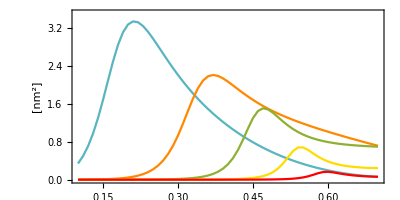

```mathematica
seccTransAn1=ListLinePlot[{Style[an1,RGBColor[0.349,0.71,0.749]],Style[an2,RGBColor[1,0.533,0]],Style[an3],Style[an4,RGBColor[1,0.863,0]],Style[an5,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["[nm^2]",Magnification->1.5],None},{Style[MaTeX["\omega/ \omega_p"],Magnification->1.5],None}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,None}},PlotRange->{{0.1,0.7},{0,3.5}},PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["l=1"],MaTeX["l=2"],MaTeX["l=3"],MaTeX["l=4"],MaTeX["l=5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1/2]
```

```mathematica
Export["seccTransAn1.svg",seccTransAn1]
```

seccTransAn1.svg

```mathematica
an11=Table[{W,mieSeccTransAn[1.5,W,1][[3]]},{W,0.1,1,0.01}];
an22=Table[{W,mieSeccTransAn[1.5,W,2][[3]]},{W,0.1,1,0.01}];
an33=Table[{W,mieSeccTransAn[1.5,W,3][[3]]},{W,0.1,1,0.01}];
an44=Table[{W,mieSeccTransAn[1.5,W,4][[3]]},{W,0.1,1,0.01}];
an55=Table[{W,mieSeccTransAn[1.5,W,5][[3]]},{W,0.1,1,0.01}];
```

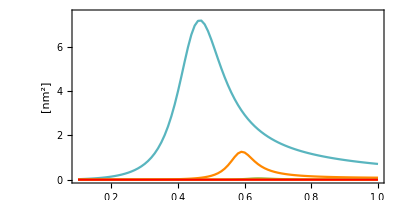

```mathematica
seccTransAn2=ListLinePlot[{Style[an11,RGBColor[0.349,0.71,0.749]],Style[an22,RGBColor[1,0.533,0]],Style[an33],Style[an44,RGBColor[1,0.863,0]],Style[an55,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["[nm^2]",Magnification->1.5],None},{Style[MaTeX["\omega/ \omega_p"],Magnification->1.5],None}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,None}},PlotRange->{{0.1,1},{0,7.5}},PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["l=1"],MaTeX["l=2"],MaTeX["l=3"],MaTeX["l=4"],MaTeX["l=5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1/2]
```

```mathematica
Export["seccTransAn2.svg",seccTransAn2]
```

seccTransAn2.svg

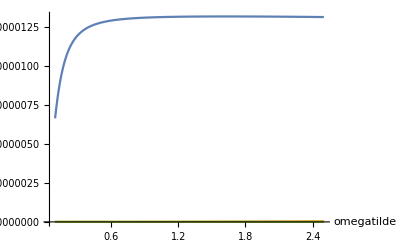

```mathematica
result3=Table[{W,mieSeccTransBn[0.1,W,#][[3]]},{W,0.1,2.5,0.01}]&/@{1,2,3};
ListLinePlot[result3,AxesLabel->{"omegatilde",""},PlotRange->All]
```

```mathematica
GoldenSearchMax[anc_,lower_,upper_,n_]:=Module[{a=N[lower],b=N[upper],c,d},k=0;
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[mieSeccTrans[anc,c,n][[4]]>mieSeccTrans[anc,d,n][[4]],(*Then*)b=d(*Else*); k=k+1;,a=c;k++;]];Return[(b+a)/2]];
```

```mathematica
ω1=Table[{anc,GoldenSearchMax[anc,0.1,1,1]},{anc,0.1,8,0.01}];
```

```mathematica
ω2=Table[{anc,GoldenSearchMax[anc,0.1,1,2]},{anc,0.1,8,0.01}];
```

```mathematica
ω3=Table[{anc,GoldenSearchMax[anc,0.1,1,3]},{anc,0.1,8,0.01}];
```

```mathematica
ω4=Table[{anc,GoldenSearchMax[anc,0.1,0.7,4]},{anc,0.1,8,0.01}];
```

```mathematica
ω5=Table[{anc,GoldenSearchMax[anc,0.1,0.7,5]},{anc,0.1,8,0.01}];
```

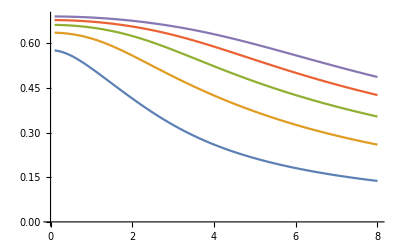

```mathematica
ListLinePlot[{ω1,ω2,ω3,ω4,ω5},PlotRange->All]
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"C:\\Users\\Lunita\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.03.1\\bin\\gswin64c.exe"
]
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
MaTeX["x^2"]
```

-Graphics-

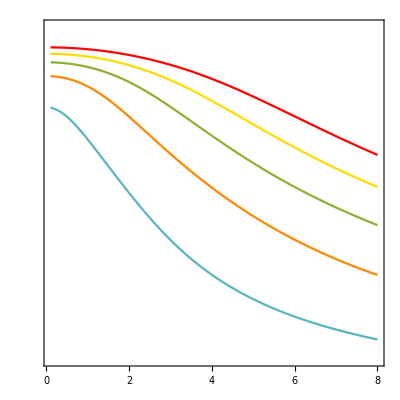

```mathematica
electricResonances=ListLinePlot[{Style[ω1,RGBColor[0.349,0.71,0.749]],Style[ω2,RGBColor[1,0.533,0]],Style[ω3],Style[ω4,RGBColor[1,0.863,0]],Style[ω5,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["\omega_l/ \omega_p"],Magnification->1.5],None},{Style[MaTeX["a\omega_p/c"],Magnification->1.5],None}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{None,All},{Automatic,None}},PlotRange->{{0.1,8},{0.1,0.73}},PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["l=1"],MaTeX["l=2"],MaTeX["l=3"],MaTeX["l=4"],MaTeX["l=5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1]
```

```mathematica
Export["ElectricResonances.svg",electricResonances]
```

ElectricResonances.svg

```mathematica
mieSeccTransBn[A_,W_,n_]:=Module[{np,m,x,bn,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[bn] ^2));
Qext =(2)/(W A)^2*((2 n +1)Re[bn]);

{bn,Qsca,Qext}]
```

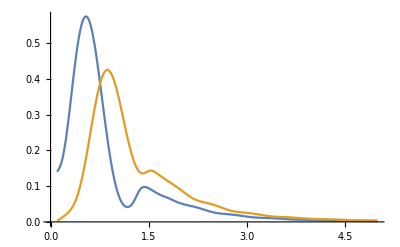

```mathematica
result3=Table[{W,mieSeccTransBn[5,W,#][[3]]},{W,0.1,5,0.01}]&/@{1,2};
ListLinePlot[result3,AxesLabel->{"",""},PlotRange->All]
```

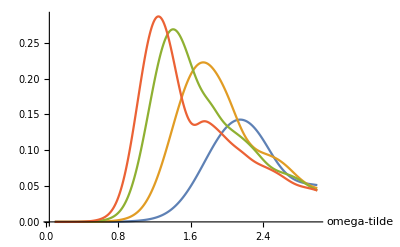

```mathematica
resultBn2=Table[{W,mieSeccTransBn[#,W,5][[3]]},{W,0.1,3,0.01}]&/@{4,5,6,6.64};
ListLinePlot[resultBn2,AxesLabel->{"omega-tilde",""},PlotRange->All]
```

```mathematica
resBn=10^{-9};
```

```mathematica
GoldenSearchMaxBn[anc_,lower_,upper_,n_]:=Module[{a=N[lower],b=N[upper],c,d},k=0;
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[mieSeccTransBn[anc,c,n][[3]]>mieSeccTransBn[anc,d,n][[3]],(*Then*)b=d(*Else*); k=k+1;,a=c;k++;]];Return[(b+a)/2]];
```

```mathematica
GoldenSearchMaxBn[4.98,0.1,1,1]
```

0.544471

```mathematica
ω1Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,5,1]},{anc,1,4.97,0.01}];
ω12Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,0.7,1]},{anc,4.98,8,0.01}];
```

```mathematica
ω2Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,5,2]},{anc,1,5,0.01}];
ω21Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,1,2]},{anc,5.01,8,0.01}];
```

```mathematica
ω3Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,5.5,3]},{anc,1,5.9,0.01}];
ω31Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,1,3]},{anc,5.91,8,0.01}];
```

```mathematica
ω4Bn=Table[{anc,GoldenSearchMaxBn[anc,0.5,7,4]},{anc,1,6.63,0.01}];
ω41Bn=Table[{anc,GoldenSearchMaxBn[anc,0.5,1.4,4]},{anc,6.64,7.5,0.01}];
```

```mathematica
ω5Bn=Table[{anc,GoldenSearchMaxBn[anc,0.05,9,5]},{anc,1,7.5,0.01}];
```

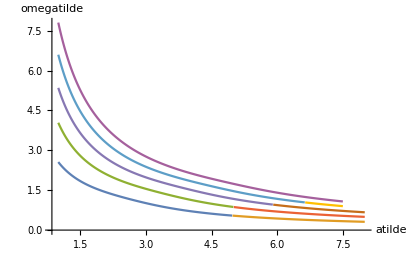

```mathematica
magneticResonances=ListLinePlot[{ω1Bn,ω12Bn,ω2Bn,ω21Bn,ω3Bn,ω31Bn,ω4Bn,ω41Bn,ω5Bn},AxesLabel->{"atilde","omegatilde"},PlotRange->All]
```

```mathematica
ColorData[97,"ColorList"]//InputForm
```

{RGBColor[0.368417, 0.506779, 0.709798], RGBColor[0.880722, 0.611041, 0.142051], RGBColor[0.560181, 0.691569, 0.194885], 
 RGBColor[0.922526, 0.385626, 0.209179], RGBColor[0.528488, 0.470624, 0.701351], RGBColor[0.772079, 0.431554, 0.102387], 
 RGBColor[0.363898, 0.618501, 0.782349], RGBColor[1, 0.75, 0], RGBColor[0.647624, 0.37816, 0.614037], 
 RGBColor[0.571589, 0.586483, 0.], RGBColor[0.915, 0.3325, 0.2125], RGBColor[0.40082222609352647, 0.5220066643438841, 
  0.85], RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142], 
 RGBColor[0.736782672705901, 0.358, 0.5030266573755369], RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

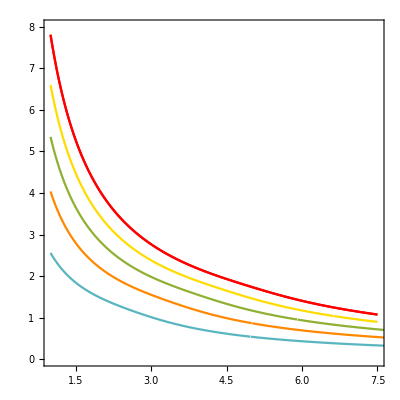

```mathematica
magneticResonances=ListLinePlot[{Style[ω1Bn,RGBColor[0.349,0.71,0.749]],Style[ω2Bn,RGBColor[1,0.533,0]],Style[ω3Bn],Style[ω4Bn,RGBColor[1,0.863,0]],Style[ω5Bn,Red],Style[ω12Bn,RGBColor[0.349,0.71,0.749]],Style[ω21Bn,RGBColor[1,0.533,0]],Style[ω31Bn,RGBColor[0.560181,0.691569,0.194885]],Style[ω41Bn,RGBColor[1,0.863,0]],Style[ω5Bn,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["\omega_l/ \omega_p"],Magnification->1.5],None},{Style[MaTeX["a\omega_p/c"],Magnification->1.5],None}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,None}},PlotRange->{{1,7.5},{0,8}},PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["l=1"],MaTeX["l=2"],MaTeX["l=3"],MaTeX["l=4"],MaTeX["l=5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1]
```

```mathematica
Export["MagneticResonances.svg",magneticResonances]
```

```mathematica
bn1=Table[{W,mieSeccTransBn[5,W,1][[3]]},{W,0.1,2.5,0.01}];
bn2=Table[{W,mieSeccTransBn[5,W,2][[3]]},{W,0.1,2.5,0.01}];
bn3=Table[{W,mieSeccTransBn[5,W,3][[3]]},{W,0.1,2.5,0.01}];
bn4=Table[{W,mieSeccTransBn[5,W,4][[3]]},{W,0.1,2.5,0.01}];
bn5=Table[{W,mieSeccTransBn[5,W,5][[3]]},{W,0.1,2.5,0.01}];
```

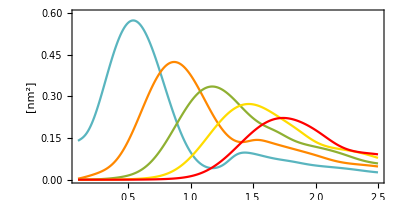

```mathematica
seccTransBn1=ListLinePlot[{Style[bn1,RGBColor[0.349,0.71,0.749]],Style[bn2,RGBColor[1,0.533,0]],Style[bn3],Style[bn4,RGBColor[1,0.863,0]],Style[bn5,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["[nm^2]",Magnification->1.5],None},{Style[MaTeX["\omega/ \omega_p"],Magnification->1.5],None}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,None}},PlotRange->{{0.1,2.5},{0,0.6}},PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["l=1"],MaTeX["l=2"],MaTeX["l=3"],MaTeX["l=4"],MaTeX["l=5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1/2]
```

```mathematica
Export["seccTransBn1.svg",seccTransBn1]
```

seccTransBn1.svg

```mathematica
bn11=Table[{W,mieSeccTransBn[1.5,W,1][[3]]},{W,1,7,0.01}];
bn22=Table[{W,mieSeccTransBn[1.5,W,2][[3]]},{W,1,7,0.01}];
bn33=Table[{W,mieSeccTransBn[1.5,W,3][[3]]},{W,1,7,0.01}];
bn44=Table[{W,mieSeccTransBn[1.5,W,4][[3]]},{W,1,7,0.01}];
bn55=Table[{W,mieSeccTransBn[1.5,W,5][[3]]},{W,1,7,0.01}];
```

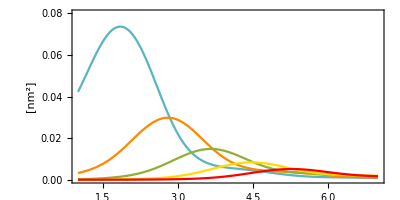

```mathematica
seccTransBn2=ListLinePlot[{Style[bn11,RGBColor[0.349,0.71,0.749]],Style[bn22,RGBColor[1,0.533,0]],Style[bn33],Style[bn44,RGBColor[1,0.863,0]],Style[bn55,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["[nm^2]",Magnification->1.5],None},{Style[MaTeX["\omega/ \omega_p"],Magnification->1.5],None}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,None}},PlotRange->{{1,7},{0,0.08}},PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["l=1"],MaTeX["l=2"],MaTeX["l=3"],MaTeX["l=4"],MaTeX["l=5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1/2]
```

```mathematica
Export["seccTransBn2.svg",seccTransBn2]
```

seccTransBn2.svg